5. domaca zadaca  								Ivan Lakovic

```mathematica
podaci = {{4.6, 0.0016308}, {5.7, 0.0032148}, {6.7, 0.005614}, {7.9, 0.0118598}, {8.8, 0.02015}, {9.8, 0.027538}, {11, 0.034546}, {12, 0.06608}, {12.9, 0.078932}, {15.2, 0.155}}
```

{{4.6,0.0016308},{5.7,0.0032148},{6.7,0.005614},{7.9,0.0118598},{8.8,0.02015},{9.8,0.027538},{11,0.034546},{12,0.06608},{12.9,0.078932},{15.2,0.155}}

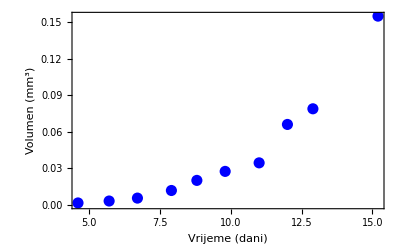

```mathematica
graf = ListPlot[podaci,Frame->True,FrameLabel->{"Vrijeme (dani)","Volumen (mm^3)"},RotateLabel->True, PlotStyle->{PointSize[0.02],RGBColor[0,0,1]}]
```

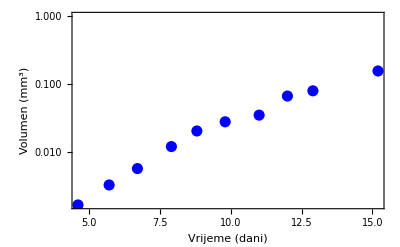

```mathematica
graf2 = ListLogPlot[podaci,Frame->True,FrameLabel->{"Vrijeme (dani)","Volumen (mm^3)"},RotateLabel->True, PlotStyle->{PointSize[0.02],RGBColor[0,0,1]}]
```

Da bi dobili pravac od eksp. funkcije logaritmiramo vrijednosti funkcije

```mathematica
promjenjena = Transpose[podaci]
```

{{4.6,5.7,6.7,7.9,8.8,9.8,11,12,12.9,15.2},{0.0016308,0.0032148,0.005614,0.0118598,0.02015,0.027538,0.034546,0.06608,0.078932,0.155}}

```mathematica
vrijednosti = promjenjena[[2]]
```

{0.0016308,0.0032148,0.005614,0.0118598,0.02015,0.027538,0.034546,0.06608,0.078932,0.155}

```mathematica
logaritmiranevrijednosti = Log[vrijednosti]
```

{-6.41868,-5.73999,-5.18249,-4.4346,-3.90455,-3.59219,-3.36546,-2.71689,-2.53917,-1.86433}

```mathematica
novipodaci = Transpose[{promjenjena[[1]], logaritmiranevrijednosti}]
```

{{4.6,-6.41868},{5.7,-5.73999},{6.7,-5.18249},{7.9,-4.4346},{8.8,-3.90455},{9.8,-3.59219},{11,-3.36546},{12,-2.71689},{12.9,-2.53917},{15.2,-1.86433}}

```mathematica
y[x_]=Fit[novipodaci,{1,x},x]
```

-8.04273+0.429904 x

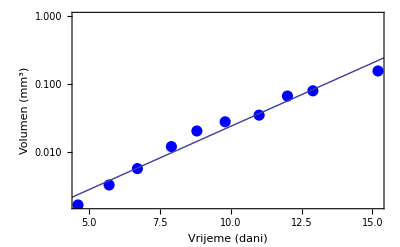

```mathematica
Show[ListLogPlot[podaci,Frame->True,FrameLabel->{"Vrijeme (dani)","Volumen (mm^3)"},RotateLabel->True, PlotStyle->{PointSize[0.02],RGBColor[0,0,1]}],Plot[-8.042728189360952+0.4299041426385786 x,{x,4,16}]]
```

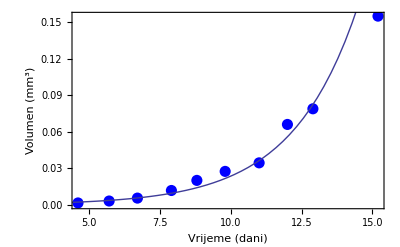

```mathematica
Show[ListPlot[podaci,Frame->True,FrameLabel->{"Vrijeme (dani)","Volumen (mm^3)"},RotateLabel->True, PlotStyle->{PointSize[0.02],RGBColor[0,0,1]}],Plot[Exp[-8.042728189360952+0.4299041426385786 x],{x,4,16}]]
```

Vrijeme udvostrucenja je:
2 = e ^ (-8.042728189360952+0.4299041426385786 x2) / e^ (-8.042728189360952+0.4299041426385786 x1)
x2 - x1 = ln2 / 0.4299041426385786 = 1.61
Broj stanica se udvostruci za 1.61 dana